```mathematica
Clear[b,α, Δ, p, f, t,s,b];
f[α_,Δ_,p_,k_] = 1/(8α(1/k-α(1/k+1/p+4/p^2+ Δ/2)))
```

1/(8 α (1/k-α (1/k+4/p^2+1/p+Δ/2)))

```mathematica
t[α_,Δ_,p_,k_]= D[f[α,Δ,p,k], α]
```

-1/(8 α^2 (1/k-α (1/k+4/p^2+1/p+Δ/2)))-(-1/k-4/p^2-1/p-Δ/2)/(8 α (1/k-α (1/k+4/p^2+1/p+Δ/2))^2)

```mathematica
b[Δ_, p_,k_] =α/.Solve[t[α,Δ,p,k]==0,α][[1,1]]
```

p^2/(8 k+2 k p+2 p^2+k p^2 Δ)

```mathematica
Reduce[b[Δ,p,k] < 2/(k * (1/k+1/p+4/p^2+ Δ/2)) && Δ>0 && k>=1 &&p>=1]
```

p≥1&&k≥1&&Δ>0

```mathematica
s[Δ_, p_,k_] = f[b[Δ, p,k], Δ, p,k] //FullSimplify
```

(k (2 p^2+k (8+p (2+p Δ))))/(4 p^2)

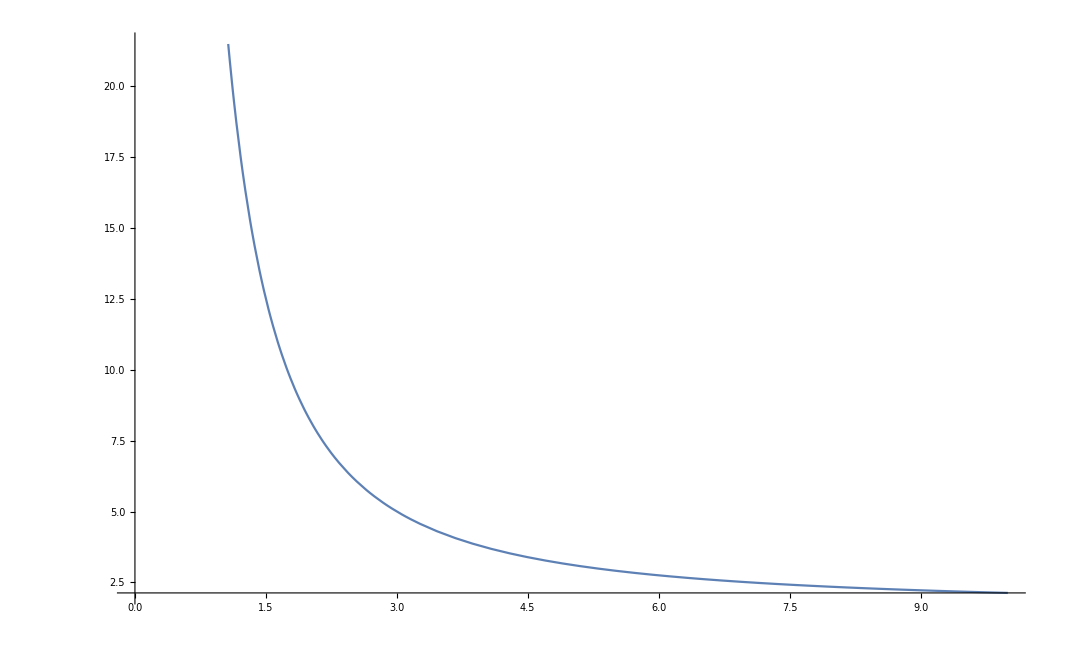

```mathematica
Plot[s[0.001,p,3],{p,0,10}]
```

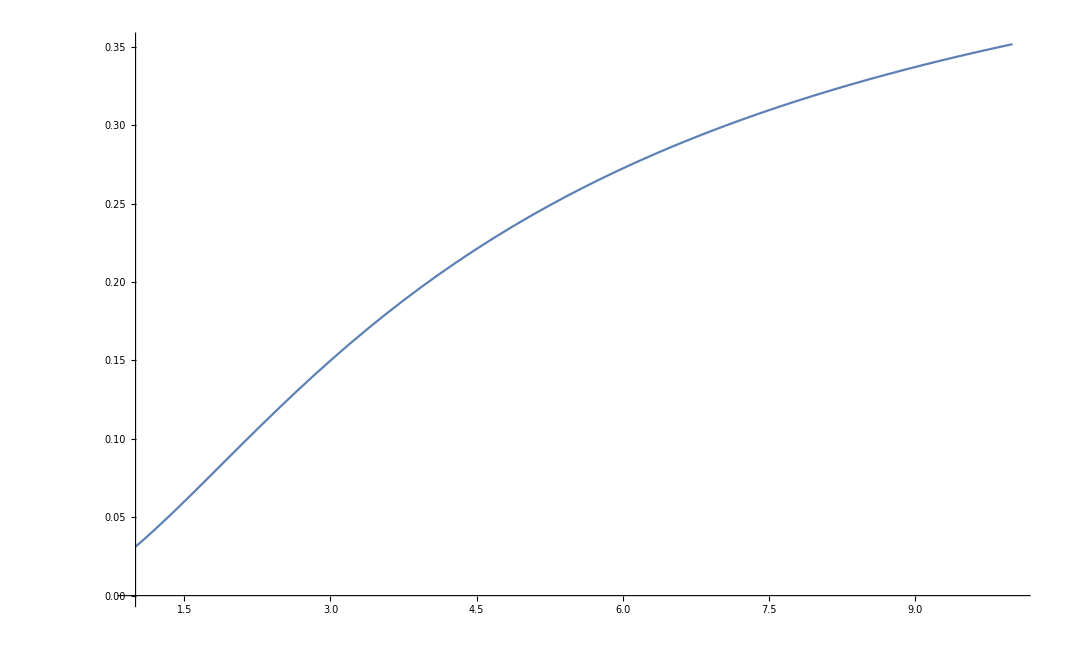

```mathematica
Plot[b[0.001,p,3],{p,1,10}]
```

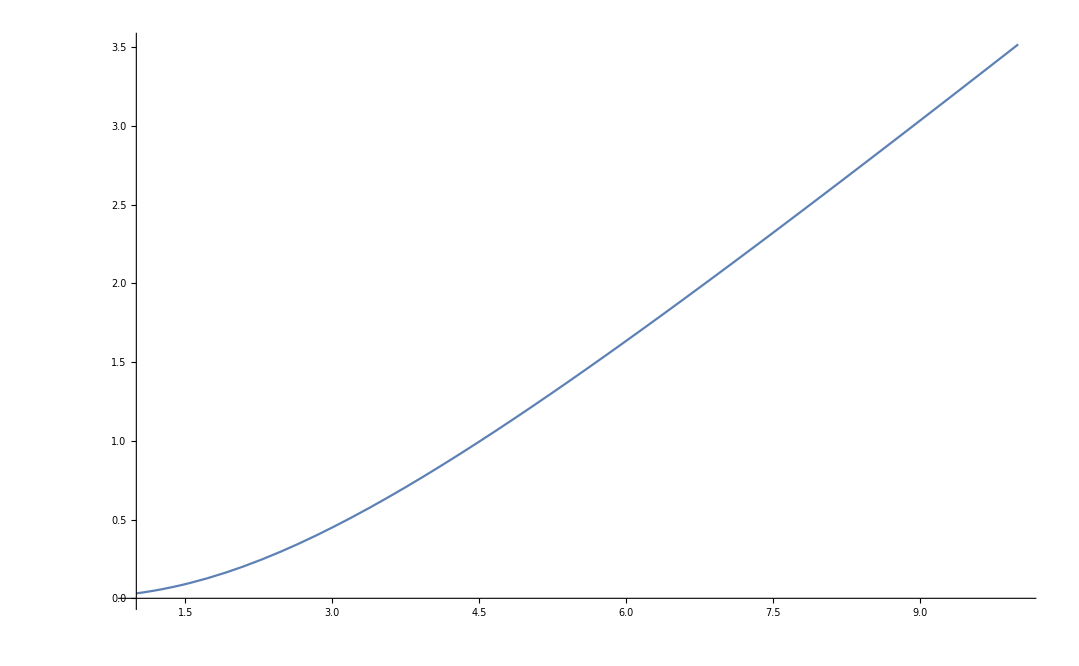

```mathematica
Plot[b[0.001,p,3]*p,{p,1,10}]
```

```mathematica
gain[Δ_,k_] = Expand[s[Δ,k,k]/Limit[s[Δ,p,k],p->+Infinity]]
```

8/(2 k+k^2 Δ)+(4 k)/(2 k+k^2 Δ)+(k^2 Δ)/(2 k+k^2 Δ)

```mathematica
Limit[gain[0,k], k->+Infinity]
```

2

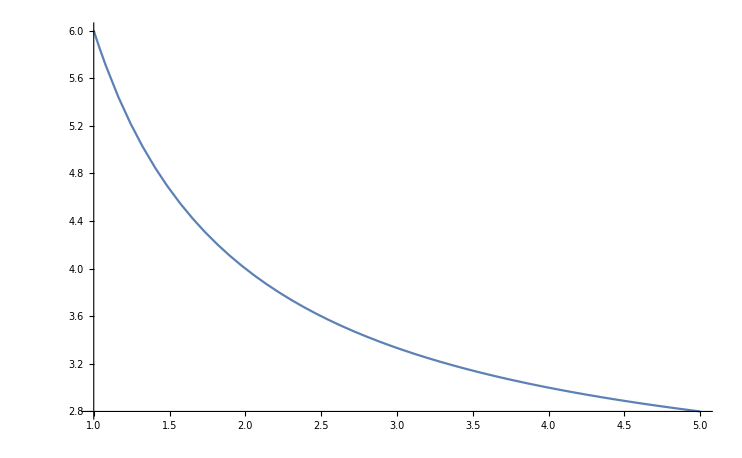

```mathematica
Plot[gain[0,k], {k,1,5}]
```